```mathematica
λ[ω_,δ_,t_,ϵ_]:=λ[ω,δ,t,ϵ]=(ω+ⅈ*δ-ϵ)IdentityMatrix[1]
```

```mathematica
T2[t_]:=T2[t]= t*IdentityMatrix[1]
```

```mathematica
T1[t_]:=T1[t]=t*IdentityMatrix[1]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[λ[ω,δ,1,0]],B:=Inverse[λ[ω,δ,1,0]],T:=T1[1]},Do[J=Inverse[IdentityMatrix[1]-B.T.J.T].B,1000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[λ[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]]
```

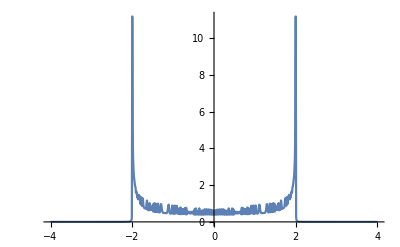

```mathematica
ListLinePlot[Table[{ω,-Im[IL[ω,0.001,1,0][[1,1]]]},{ω,Range[-4,4,0.01]}],PlotRange->All]
```

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_]:= Inverse[(ω+ⅈ*δ-ϵ1)IdentityMatrix[1]]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{gg=g[ω,δ,t,ϵ],T=t*IdentityMatrix[1],imp=imp[ω,δ,t,ϵ,ϵ1]},sl1= Module[{J=SL[ω,δ,1,0],n=RandomInteger[{0,20}]},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,n]; J=J];sl2=Inverse[IdentityMatrix[1]-imp.T.sl1.T].imp; sl3=Module[{J=sl2,m=RandomInteger[{0,20}]},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,m]; J=J];sl4=Inverse[IdentityMatrix[1]-imp.T.sl3.T].imp; sl5=Module[{J=sl4,o=RandomInteger[{0,20}]},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,o]; J=J];sl6=Inverse[IdentityMatrix[1]-imp.T.sl5.T].imp; sl7=Module[{J=sl6,p=RandomInteger[{0,20}]},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,p]; J=J];sl8=Inverse[IdentityMatrix[1]-imp.T.sl7.T].imp; sl9=Module[{J=sl8,q=RandomInteger[{0,20}]},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,q]; J=J];sl10=Inverse[IdentityMatrix[1]-imp.T.sl9.T].imp; sl11=Module[{J=sl10,r=RandomInteger[{0,20}]},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,r]; J=J];sl12=Inverse[IdentityMatrix[1]-imp.T.sl11.T].imp; sl13=Module[{J=sl12,s=RandomInteger[{0,20}]},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,s]; J=J];sl14=Inverse[IdentityMatrix[1]-imp.T.sl13.T].imp; sl15=Module[{J=sl14,v=RandomInteger[{0,20}]},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,v]; J=J];Il1:=Inverse[IdentityMatrix[1]-sl15.T1[1].SR[ω,δ,1,0].T1[1]].sl15;Ir1:=Inverse[IdentityMatrix[1]-SR[ω,δ,1,0].T1[1].sl15.T1[1]].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].T1[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
tr1[1,0.001,1,0,0]
```

0.73604

```mathematica
8Mean[Table[RandomInteger[{0,20}],1000]]
```

9722/125

```mathematica
N[10114/125]
```

80.912

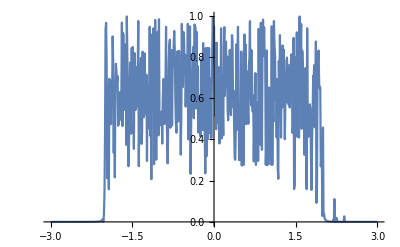

```mathematica
ListLinePlot[Table[{ω,tr1[ω,0.01,1,0,1]},{ω,Range[-3,3,0.01]}]]
```

```mathematica
Mean[Table[tr1[.04,0.001,1,0,1],20000]]
```

0.413839

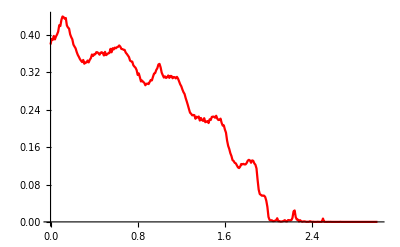

```mathematica
ListLinePlot[Import["/home/shardulmukim/PhD/fwi/1D/1d7imp1.csv"],PlotStyle->Red]
```

```mathematica
ListLinePlot[Table[{ω,Mean[Table[tr1[ω,0.001,1,0,1],10000]]},{ω,Range[-3,3,0.01]}]]
```

```mathematica
Export["1d7imp1.csv",f[1]]
```

1d7imp1.csv

```mathematica
Export["1d7imp3.csv",f[0.3]]
```

1d7imp3.csv

```mathematica
Export["1d7imp4.csv",f[0.4]]
```

1d7imp4.csv

```mathematica
Export["1d7imp5.csv",f[0.5]]
```

1d7imp5.csv

```mathematica
Export["1d7imp6.csv",f[0.6]]
```

1d7imp6.csv

```mathematica
Export["1d7imp7.csv",f[0.7]]
```

1d7imp7.csv

```mathematica
Export["1d7imp8.csv",f[0.8]]
```

1d7imp8.csv

```mathematica
Export["1d7imp9.csv",f[.9]]
```

1d7imp9.csv

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
ψ[ω_,δ_,t_,ϵ_,m_]:= ReplacePart[β[ω,δ,t,ϵ,m],{{1,1},{m,m}}->ω+ⅈ*δ-Im[SL[ω,0.01,1,0]][[1,1]]]
```

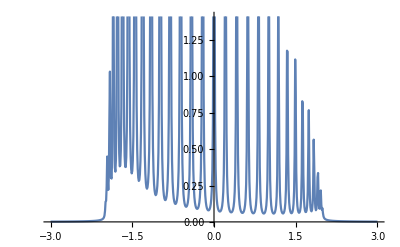

```mathematica
ListLinePlot[Table[{ω,-Im[Inverse[ψ[ω,0.01,1,0,30]][[1,1]]]},{ω,Range[-3,3,0.01]}]]
```

```mathematica
Table[{ω,-Im[Inverse[ψ[ω,0.01,1,0,10]][[2,2]]]},{ω,Range[-3,3,0.01]}]
```

{{-3.,0.00245641},{-2.99,0.00248919},{-2.98,0.00252269},{-2.97,0.00255695},{-2.96,0.00259197},{-2.95,0.0026278},{-2.94,0.00266444},{-2.93,0.00270194},{-2.92,0.00274031},{-2.91,0.00277959},{-2.9,0.00281981},{-2.89,0.002861},{-2.88,0.00290319},{-2.87,0.00294642},{-2.86,0.00299072},{-2.85,0.00303614},{-2.84,0.00308271},{-2.83,0.00313047},{-2.82,0.00317947},{-2.81,0.00322975},{-2.8,0.00328136},{-2.79,0.00333436},{-2.78,0.00338879},{-2.77,0.00344471},{-2.76,0.00350218},{-2.75,0.00356126},{-2.74,0.00362202},{-2.73,0.00368452},{-2.72,0.00374884},{-2.71,0.00381505},{-2.7,0.00388322},{-2.69,0.00395346},{-2.68,0.00402584},{-2.67,0.00410046},{-2.66,0.00417741},{-2.65,0.00425682},{-2.64,0.00433878},{-2.63,0.00442341},{-2.62,0.00451085},{-2.61,0.00460123},{-2.6,0.00469468},{-2.59,0.00479136},{-2.58,0.00489144},{-2.57,0.00499509},{-2.56,0.00510248},{-2.55,0.00521383},{-2.54,0.00532933},{-2.53,0.00544922},{-2.52,0.00557373},{-2.51,0.00570313},{-2.5,0.00583771},{-2.49,0.00597775},{-2.48,0.00612359},{-2.47,0.00627557},{-2.46,0.00643409},{-2.45,0.00659954},{-2.44,0.00677237},{-2.43,0.00695308},{-2.42,0.00714219},{-2.41,0.00734027},{-2.4,0.00754795},{-2.39,0.00776593},{-2.38,0.00799495},{-2.37,0.00823585},{-2.36,0.00848955},{-2.35,0.00875705},{-2.34,0.00903947},{-2.33,0.00933806},{-2.32,0.00965419},{-2.31,0.00998941},{-2.3,0.0103455},{-2.29,0.0107243},{-2.28,0.011128},{-2.27,0.0115592},{-2.26,0.0120206},{-2.25,0.0125155},{-2.24,0.0130475},{-2.23,0.0136208},{-2.22,0.0142403},{-2.21,0.0149117},{-2.2,0.0156417},{-2.19,0.0164379},{-2.18,0.0173098},{-2.17,0.0182681},{-2.16,0.0193261},{-2.15,0.0204998},{-2.14,0.0218087},{-2.13,0.0232768},{-2.12,0.0249339},{-2.11,0.0268178},{-2.1,0.0289767},{-2.09,0.0314728},{-2.08,0.0343883},{-2.07,0.0378332},{-2.06,0.0419582},{-2.05,0.0469754},{-2.04,0.0531928},{-2.03,0.061078},{-2.02,0.071393},{-2.01,0.0855572},{-2.,0.106836},{-1.99,0.140952},{-1.98,0.195702},{-1.97,0.290615},{-1.96,0.477666},{-1.95,0.921747},{-1.94,2.28091},{-1.93,5.77078},{-1.92,3.42455},{-1.91,1.30637},{-1.9,0.658122},{-1.89,0.411453},{-1.88,0.299497},{-1.87,0.244926},{-1.86,0.220352},{-1.85,0.215125},{-1.84,0.225786},{-1.83,0.253281},{-1.82,0.303052},{-1.81,0.38781},{-1.8,0.535809},{-1.79,0.815579},{-1.78,1.4231},{-1.77,3.07439},{-1.76,9.02067},{-1.75,14.899},{-1.74,5.14328},{-1.73,2.05278},{-1.72,1.07042},{-1.71,0.658225},{-1.7,0.450394},{-1.69,0.332286},{-1.68,0.25956},{-1.67,0.212326},{-1.66,0.180668},{-1.65,0.159256},{-1.64,0.145094},{-1.63,0.136486},{-1.62,0.132547},{-1.61,0.132978},{-1.6,0.138005},{-1.59,0.148456},{-1.58,0.166016},{-1.57,0.193801},{-1.56,0.237612},{-1.55,0.308856},{-1.54,0.432073},{-1.53,0.667409},{-1.52,1.19265},{-1.51,2.69167},{-1.5,8.21189},{-1.49,9.75784},{-1.48,3.14867},{-1.47,1.30913},{-1.46,0.698008},{-1.45,0.432596},{-1.44,0.295324},{-1.43,0.215531},{-1.42,0.165145},{-1.41,0.131315},{-1.4,0.107507},{-1.39,0.0901213},{-1.38,0.0770421},{-1.37,0.0669618},{-1.36,0.0590393},{-1.35,0.052714},{-1.34,0.0476013},{-1.33,0.0434309},{-1.32,0.0400097},{-1.31,0.0371984},{-1.3,0.0348965},{-1.29,0.0330329},{-1.28,0.0315592},{-1.27,0.0304468},{-1.26,0.0296857},{-1.25,0.0292857},{-1.24,0.0292801},{-1.23,0.0297343},{-1.22,0.0307603},{-1.21,0.0325451},{-1.2,0.0354023},{-1.19,0.0398773},{-1.18,0.0469718},{-1.17,0.05867},{-1.16,0.0793348},{-1.15,0.120024},{-1.14,0.21492},{-1.13,0.499565},{-1.12,1.35466},{-1.11,0.926484},{-1.1,0.326403},{-1.09,0.152417},{-1.08,0.0883518},{-1.07,0.058748},{-1.06,0.0428246},{-1.05,0.0333137},{-1.04,0.0271851},{-1.03,0.0230029},{-1.02,0.0200182},{-1.01,0.0178106},{-1.,0.0161304},{-0.99,0.0148225},{-0.98,0.0137864},{-0.97,0.0129541},{-0.96,0.012278},{-0.95,0.0117238},{-0.94,0.0112674},{-0.93,0.0108919},{-0.92,0.010585},{-0.91,0.010337},{-0.9,0.0101402},{-0.89,0.00998925},{-0.88,0.00988117},{-0.87,0.00981404},{-0.86,0.00978649},{-0.85,0.0097984},{-0.84,0.00985119},{-0.83,0.00994714},{-0.82,0.0100896},{-0.81,0.0102841},{-0.8,0.0105384},{-0.79,0.0108608},{-0.78,0.0112638},{-0.77,0.0117664},{-0.76,0.0123922},{-0.75,0.013169},{-0.74,0.0141419},{-0.73,0.015379},{-0.72,0.0169657},{-0.71,0.0190291},{-0.7,0.0217898},{-0.69,0.0255867},{-0.68,0.0309531},{-0.67,0.0389059},{-0.66,0.05144},{-0.65,0.0726027},{-0.64,0.112293},{-0.63,0.199606},{-0.62,0.437679},{-0.61,1.18351},{-0.6,1.35769},{-0.59,0.513667},{-0.58,0.228646},{-0.57,0.126973},{-0.56,0.0816906},{-0.55,0.0580372},{-0.54,0.0441804},{-0.53,0.0354426},{-0.52,0.0296125},{-0.51,0.0255389},{-0.5,0.0226095},{-0.49,0.0204507},{-0.48,0.0188302},{-0.47,0.0176025},{-0.46,0.0166674},{-0.45,0.0159581},{-0.44,0.015425},{-0.43,0.0150356},{-0.42,0.0147659},{-0.41,0.0145944},{-0.4,0.0145127},{-0.39,0.0145084},{-0.38,0.0145737},{-0.37,0.0147093},{-0.36,0.0149061},{-0.35,0.0151668},{-0.34,0.0154937},{-0.33,0.0158811},{-0.32,0.0163412},{-0.31,0.0168723},{-0.3,0.0174791},{-0.29,0.0181778},{-0.28,0.0189643},{-0.27,0.0198615},{-0.26,0.0208802},{-0.25,0.0220287},{-0.24,0.0233469},{-0.23,0.0248391},{-0.22,0.0265511},{-0.21,0.0285258},{-0.2,0.0307907},{-0.19,0.0334466},{-0.18,0.0365384},{-0.17,0.0401916},{-0.16,0.0445616},{-0.15,0.0497828},{-0.14,0.0561941},{-0.13,0.064072},{-0.12,0.0739641},{-0.11,0.0866629},{-0.1,0.103138},{-0.09,0.125402},{-0.08,0.156075},{-0.07,0.200274},{-0.06,0.26741},{-0.05,0.375079},{-0.04,0.566173},{-0.03,0.944994},{-0.02,1.84661},{-0.01,4.52074},{0.,9.86557},{0.01,5.50458},{0.02,2.17176},{0.03,1.06881},{0.04,0.624088},{0.05,0.4085},{0.06,0.288088},{0.07,0.215129},{0.08,0.16743},{0.09,0.134681},{0.1,0.111372},{0.11,0.094103},{0.12,0.0811036},{0.13,0.0710411},{0.14,0.063139},{0.15,0.0568685},{0.16,0.0518043},{0.17,0.0477149},{0.18,0.0443754},{0.19,0.0416463},{0.2,0.0394233},{0.21,0.0376106},{0.22,0.0361548},{0.23,0.0350006},{0.24,0.0341113},{0.25,0.0334586},{0.26,0.0330199},{0.27,0.0327786},{0.28,0.0327239},{0.29,0.0328502},{0.3,0.03315},{0.31,0.0336301},{0.32,0.0342896},{0.33,0.035136},{0.34,0.0361879},{0.35,0.0374497},{0.36,0.0389521},{0.37,0.0407202},{0.38,0.0427773},{0.39,0.0451837},{0.4,0.0479757},{0.41,0.0512218},{0.42,0.0550218},{0.43,0.0594528},{0.44,0.0646724},{0.45,0.0708595},{0.46,0.0782096},{0.47,0.087076},{0.48,0.0978495},{0.49,0.11107},{0.5,0.12762},{0.51,0.14859},{0.52,0.175688},{0.53,0.2117},{0.54,0.2607},{0.55,0.329819},{0.56,0.432043},{0.57,0.591254},{0.58,0.858792},{0.59,1.35853},{0.6,2.43429},{0.61,5.26979},{0.62,13.4846},{0.63,15.3211},{0.64,6.14352},{0.65,2.72939},{0.66,1.48342},{0.67,0.923306},{0.68,0.628541},{0.69,0.456029},{0.7,0.346986},{0.71,0.27373},{0.72,0.222264},{0.73,0.18488},{0.74,0.156906},{0.75,0.135454},{0.76,0.118718},{0.77,0.105467},{0.78,0.0948282},{0.79,0.0862022},{0.8,0.079169},{0.81,0.0734083},{0.82,0.0686761},{0.83,0.0647961},{0.84,0.0616372},{0.85,0.0590946},{0.86,0.0570871},{0.87,0.0555554},{0.88,0.054457},{0.89,0.0537601},{0.9,0.0534436},{0.91,0.0534969},{0.92,0.053919},{0.93,0.0547173},{0.94,0.0559087},{0.95,0.0575206},{0.96,0.0595926},{0.97,0.0621777},{0.98,0.0653452},{0.99,0.069186},{1.,0.0738188},{1.01,0.079399},{1.02,0.0861297},{1.03,0.0942793},{1.04,0.104207},{1.05,0.116403},{1.06,0.131545},{1.07,0.150598},{1.08,0.174961},{1.09,0.206729},{1.1,0.249146},{1.11,0.307451},{1.12,0.390534},{1.13,0.514448},{1.14,0.710506},{1.15,1.04619},{1.16,1.68732},{1.17,3.11792},{1.18,7.03445},{1.19,17.1592},{1.2,14.3603},{1.21,5.68254},{1.22,2.6581},{1.23,1.49621},{1.24,0.95283},{1.25,0.659741},{1.26,0.484944},{1.27,0.372798},{1.28,0.296793},{1.29,0.243056},{1.3,0.203783},{1.31,0.174317},{1.32,0.151745},{1.33,0.134173},{1.34,0.12033},{1.35,0.10934},{1.36,0.100586},{1.37,0.0936278},{1.38,0.088147},{1.39,0.0839153},{1.4,0.0807708},{1.41,0.0786029},{1.42,0.0773437},{1.43,0.0769625},{1.44,0.0774643},{1.45,0.0788903},{1.46,0.0813225},{1.47,0.0848924},{1.48,0.0897941},{1.49,0.0963067},{1.5,0.104828},{1.51,0.115928},{1.52,0.130437},{1.53,0.149591},{1.54,0.175285},{1.55,0.210526},{1.56,0.260319},{1.57,0.333451},{1.58,0.446475},{1.59,0.633464},{1.6,0.973174},{1.61,1.67783},{1.62,3.43877},{1.63,8.59588},{1.64,13.3906},{1.65,6.03502},{1.66,2.58307},{1.67,1.36122},{1.68,0.832165},{1.69,0.561957},{1.7,0.407045},{1.71,0.310641},{1.72,0.246969},{1.73,0.203048},{1.74,0.17181},{1.75,0.149168},{1.76,0.132661},{1.77,0.120776},{1.78,0.112597},{1.79,0.107625},{1.8,0.105695},{1.81,0.106971},{1.82,0.112026},{1.83,0.122037},{1.84,0.139228},{1.85,0.167839},{1.86,0.216437},{1.87,0.304051},{1.88,0.479005},{1.89,0.888037},{1.9,2.05805},{1.91,4.6636},{1.92,3.07356},{1.93,1.24275},{1.94,0.617767},{1.95,0.367371},{1.96,0.246124},{1.97,0.178991},{1.98,0.138208},{1.99,0.111796},{2.,0.0936001},{2.01,0.0793306},{2.02,0.067818},{2.03,0.0587477},{2.04,0.0515551},{2.05,0.0457653},{2.06,0.041031},{2.07,0.0371027},{2.08,0.0338001},{2.09,0.0309906},{2.1,0.0285754},{2.11,0.0264796},{2.12,0.0246457},{2.13,0.023029},{2.14,0.0215939},{2.15,0.0203122},{2.16,0.0191612},{2.17,0.0181223},{2.18,0.0171802},{2.19,0.0163222},{2.2,0.0155379},{2.21,0.0148183},{2.22,0.0141559},{2.23,0.0135443},{2.24,0.0129779},{2.25,0.012452},{2.26,0.0119626},{2.27,0.0115061},{2.28,0.0110792},{2.29,0.0106793},{2.3,0.010304},{2.31,0.0099511},{2.32,0.00961871},{2.33,0.00930515},{2.34,0.0090089},{2.35,0.00872861},{2.36,0.00846305},{2.37,0.00821113},{2.38,0.00797186},{2.39,0.00774432},{2.4,0.00752772},{2.41,0.0073213},{2.42,0.00712438},{2.43,0.00693635},{2.44,0.00675664},{2.45,0.00658472},{2.46,0.00642012},{2.47,0.0062624},{2.48,0.00611115},{2.49,0.005966},{2.5,0.0058266},{2.51,0.00569262},{2.52,0.00556377},{2.53,0.00543978},{2.54,0.00532038},{2.55,0.00520533},{2.56,0.00509442},{2.57,0.00498742},{2.58,0.00488416},{2.59,0.00478443},{2.6,0.00468808},{2.61,0.00459494},{2.62,0.00450486},{2.63,0.0044177},{2.64,0.00433333},{2.65,0.00425161},{2.66,0.00417245},{2.67,0.00409571},{2.68,0.0040213},{2.69,0.00394912},{2.7,0.00387907},{2.71,0.00381107},{2.72,0.00374503},{2.73,0.00368088},{2.74,0.00361853},{2.75,0.00355791},{2.76,0.00349897},{2.77,0.00344163},{2.78,0.00338583},{2.79,0.00333152},{2.8,0.00327864},{2.81,0.00322713},{2.82,0.00317695},{2.83,0.00312805},{2.84,0.00308038},{2.85,0.0030339},{2.86,0.00298857},{2.87,0.00294434},{2.88,0.00290119},{2.89,0.00285907},{2.9,0.00281796},{2.91,0.0027778},{2.92,0.00273859},{2.93,0.00270027},{2.94,0.00266284},{2.95,0.00262625},{2.96,0.00259048},{2.97,0.0025555},{2.98,0.0025213},{2.99,0.00248784},{3.,0.00245511}}

```mathematica
For
```